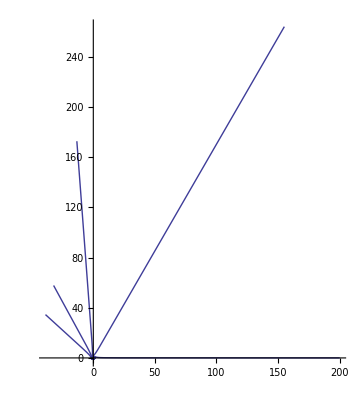

```mathematica
r[t_]:=(1+ C*Exp[-2*a*t])^{-1/2};
PolarPlot[Flatten[Table[r[t]/.{a->1/3},{C,-5,5}]],{t,-20,20}]
```

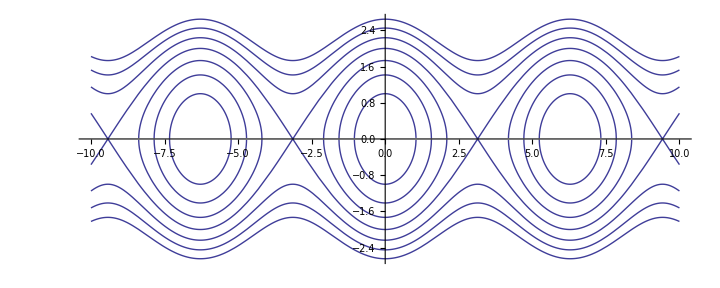

```mathematica
ParametricPlot[Flatten[Table[{{theta,Sqrt[2 a Cos[theta]+C]},{theta,-Sqrt[2 a Cos[theta] + C]}}/.a->1,{C,-5,5}]],{theta,-10,10}]
```

```mathematica
Clear[x,y,a,b]
DSolve[{x'[t]== y[t],y'[t]== -x[t](x[t]^2 -1)},{x[t],y[t]},t]
```

{{y[t]→-1/(√2)(√(4 C[1]+2 (InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(-1/(1-√(1+4 C[1]))) #1],(1-√(1+4 C[1]))/(1+√(1+4 C[1]))] √(1-#1^2/(1-√(1+4 C[1]))) √(1-#1^2/(1+√(1+4 C[1]))))/(√(-1/(1-√(1+4 C[1]))) √(4 C[1]+2 #1^2-#1^4))&][-t/(√2)+C[2]])^2-(InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(-1/(1-√(1+4 C[1]))) #1],(1-√(1+4 C[1]))/(1+√(1+4 C[1]))] √(1-#1^2/(1-√(1+4 C[1]))) √(1-#1^2/(1+√(1+4 C[1]))))/(√(-1/(1-√(1+4 C[1]))) √(4 C[1]+2 #1^2-#1^4))&][-t/(√2)+C[2]])^4)),x[t]→InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(-1/(1-√(1+4 C[1]))) #1],(1-√(1+4 C[1]))/(1+√(1+4 C[1]))] √(1-#1^2/(1-√(1+4 C[1]))) √(1-#1^2/(1+√(1+4 C[1]))))/(√(-1/(1-√(1+4 C[1]))) √(4 C[1]+2 #1^2-#1^4))&][-t/(√2)+C[2]]},{y[t]→1/(√2)(√(4 C[1]+2 (InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(-1/(1-√(1+4 C[1]))) #1],(1-√(1+4 C[1]))/(1+√(1+4 C[1]))] √(1-#1^2/(1-√(1+4 C[1]))) √(1-#1^2/(1+√(1+4 C[1]))))/(√(-1/(1-√(1+4 C[1]))) √(4 C[1]+2 #1^2-#1^4))&][t/(√2)+C[2]])^2-(InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(-1/(1-√(1+4 C[1]))) #1],(1-√(1+4 C[1]))/(1+√(1+4 C[1]))] √(1-#1^2/(1-√(1+4 C[1]))) √(1-#1^2/(1+√(1+4 C[1]))))/(√(-1/(1-√(1+4 C[1]))) √(4 C[1]+2 #1^2-#1^4))&][t/(√2)+C[2]])^4)),x[t]→InverseFunction[-(ⅈ EllipticF[ⅈ ArcSinh[√(-1/(1-√(1+4 C[1]))) #1],(1-√(1+4 C[1]))/(1+√(1+4 C[1]))] √(1-#1^2/(1-√(1+4 C[1]))) √(1-#1^2/(1+√(1+4 C[1]))))/(√(-1/(1-√(1+4 C[1]))) √(4 C[1]+2 #1^2-#1^4))&][t/(√2)+C[2]]}}

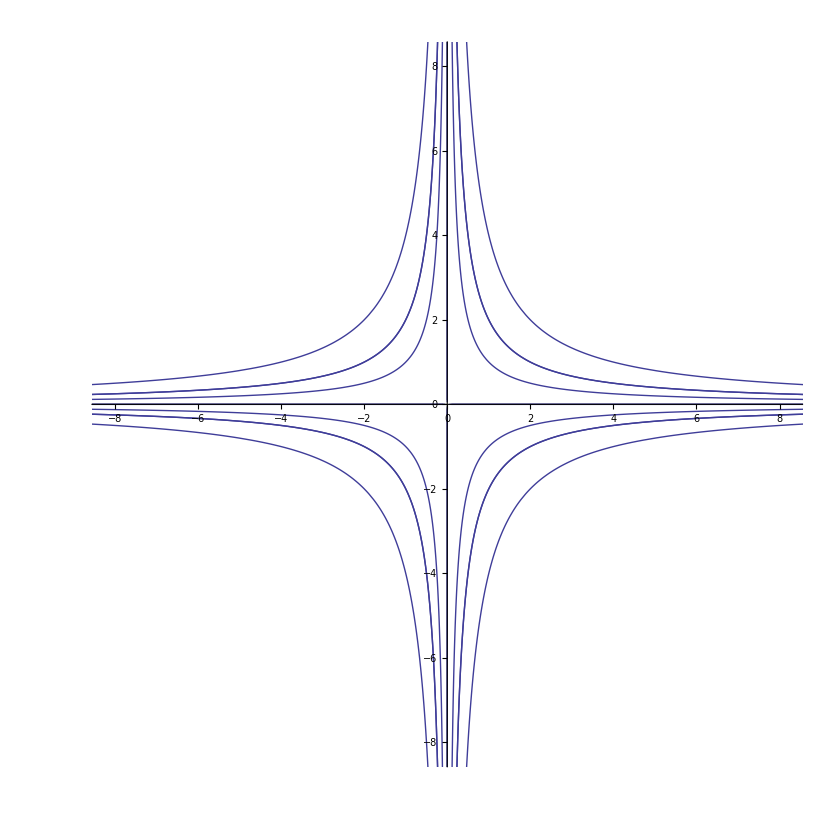

```mathematica
x[t] =  Exp[t];
y[t] =  Exp[-t];
ParametricPlot[Table[{a Exp[t],b Exp[-t]},{a,-2,2},{b,-2,2}],{t,-3,3}]
```

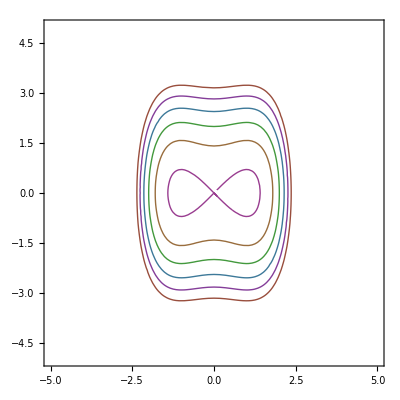

```mathematica
ContourPlot[Evaluate[Table[x^4/4-x^2/2+y^2/2 ==C,{C,-5,5}]],{x,-5,5},{y,-5,5}]
```